```mathematica
Options[Plot,DisplayFunction]
```

{DisplayFunction:>$DisplayFunction}

tip1: Display will close file that was opened, but the WriteString will not close the file automatically.

```mathematica
$DisplayFunction
```

Identity

```mathematica
$Display
```

{}

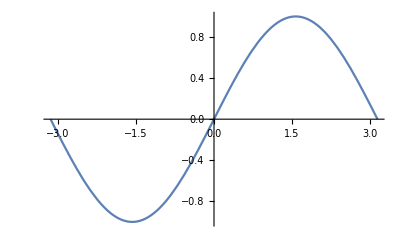

```mathematica
Plot[Sin[x],{x,-Pi,Pi},DisplayFunction->(Function[g,Export["sin.png",g];g])]
```